# Lab 15: Measuring Harmonic Motion

#### Introduction

In this lab, we will study simple harmonic by measuring the oscillations of a mass attached to a conical spring. The spring has been wound so that it has an effective spring constant k and it is attached to a block (+ a block holder) of total mass M.

We will use a range finder that emits ultra-sonic pulses to measure the distance from the box to the nearest object by measuring the time delay of the reflected pulse. If the spring were massless (as in most physics lectures), then we would expect that the angular frequency of the oscillations would be 

ω = √(k/M)  (massless spring)

For a massive spring, the angular frequency will be

ω = √(k/(M + c m_spring))

where 0 ≤ c ≤1 and m_spring is the mass of the spring.

The value of constant c depends on how the mass of the spring is distributed along the spring. In this experiment, we will measure c.

### Phase 1: Find the spring parameters

#### The Experimental Setup

Hang the spring (narrow end up) from the ring stand. Hang a weight holder from the other end of the spring and place the range finder on the ground underneath the weight holder.  You will take data by connecting the range finder to a USB interface box and using the Data Studio software.  Set the experiment up so that you get a three column list where the first column is the time data, the second column is the position data, the third column is the velocity data. Save your data as a “CSV” (“Comma Separated Values”) file.  

Use a plumb to align the weight holder and the range finder. In order to get good data, the range finder must always be a least 0.5 meters from the weight holder. Put several different weights on the mass holder and use the range finder to measure the period of oscillation for several different masses. 

Since

T=(2π)/ω
      =2π √((M + c m_spring)/k)

we can write

T^2 = 4 π^2 (M +c m_spring)/k
         = (4 π^2)/k M + 4 π^2(c m_spring)/k.

Thus, if we vary M, a plot of T^2 against M should result in a straight line with slope (4 π^2)/k and y intercept (4 π^2 c m_spring)/kThis will allow you to determine both c and k.

#### Analyzing the Data

We can import the data into Mathematica using the function Import.

This “Import” statement is not expected to work; it (and the statements below which depend on it) is (are) only included so that you see what the code looks like.  Your statements can be based on these, but will be changed somewhat.

```mathematica
experimentialData=Import["/Users/gass/Desktop/harmonic.csv"];
```

Selecting the first two columns gives us a list of time and position values.

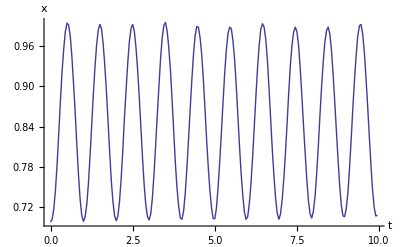

```mathematica
positionData=Table[{ experimentialData⟦i,1⟧, experimentialData⟦i,2⟧},{i,1,Length[ experimentialData]}];
ListPlot[positionData,Joined->True,AxesLabel->{"t","x"}]
```

You can read the period of the oscillation from the graph (use the Get Coordinates option on the plot by right-clicking on it).  Do this for all the different weights that you used. Some sample data is shown below. Here t1 is the square of the period obtained with weight m1 and so on. The units are SI units.

```mathematica
t1=0.8^2;
m1=0.1;
t2=1^2;
m2=0.2;
t3=1.15^2;
m3=0.3;
t4=1.3^2;
m4=0.4;
t5=1.5^2;
m5=0.5;
data={{m1,t1},{m2,t2},{m3,t3},{m4,t4},{m5,t5}};
```

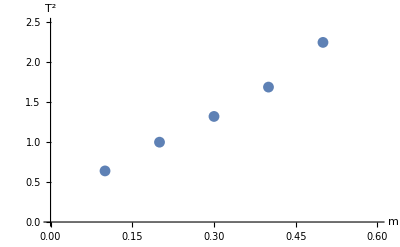

```mathematica
plot1=ListPlot[data,PlotRange->{{0,.6},{0,2.5}},AxesLabel->{"m","T^2"}]
```

We can use Fit to find the slope and y intercept.

```mathematica
fitTm=Fit[data,{1,m},m]
```

0.2075+3.91 m

We should check the fit

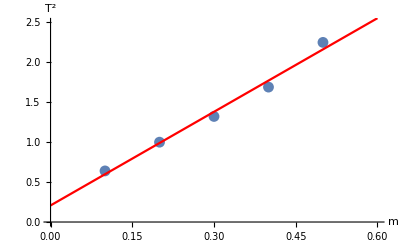

```mathematica
plot2=Plot[fitTm,{m,0,.6},PlotStyle->RGBColor[1,0,0],AxesLabel->{"m","T^2"}];
Show[plot1,plot2]
```

The slope is 3.91:

```mathematica
k=(2 π)^2/Coefficient[fitTm,m,1]
```

10.0968

The mass of the spring we used was (weigh your spring - it might not have the same mass!) m_spring=0.173 kg. Since c=(k*(y-intercept))/(4 π^2 m_spring) we have

```mathematica
c=Coefficient[fitTm,m,0] k/(4 π^2 m)/.m->.173
```

0.306758

The values of k and c may be different for your spring, although you should check to make sure your particular values are physically reasonable!

We should calculate the standard deviation of our data. Recall that the data in question is

```mathematica
data
```

{{0.1,0.64},{0.2,1},{0.3,1.3225},{0.4,1.69},{0.5,2.25}}

We can extract the period data and the mass data into separate lists using

```mathematica
mdata=data/.{x_,y_}->x
Tdata=data/.{x_,y_}->y
```

{0.1,0.2,0.3,0.4,0.5}

{0.64,1,1.3225,1.69,2.25}

The periods predicted by the fit are

```mathematica
theory=fitTm/.m->mdata
```

{0.5985,0.9895,1.3805,1.7715,2.1625}

and the standard deviation is σ=√((Σ(T_theory-T_experiment))/(N-1)); that is,

```mathematica
sd=√((Plus@@((theory-Tdata)^2))/(Length[mdata]-1))
```

0.0698122

We used the Plus@@ command, a shorthand command which adds all the elements of a list one by one.  For example, the following two statements are essentially the same, but one is much simpler:

```mathematica
Plus@@{1,2,3,4}
Sum[{1,2,3,4}[[i]],{i,1,Length[{1,2,3,4}]}]
```

10

10

-------------------------------------------------------------------------------------------------------------------------------------------------------------------------

Of course, we already know how to use some other fancy built-in fit functions, which calculate the standard deviation automatically.  Let’s compare:

```mathematica
autoFit=LinearModelFit[data,x,x]
autoFit["ParameterTable"]
autoSd=√autoFit["EstimatedVariance"]
```

FittedModel[0.2075+3.91 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.2075 | 0.0845468 | 2.45426 | 0.0913324
x | 3.91 | 0.254918 | 15.3382 | 0.000601918

0.0806122

The two standard deviations are different by about .01

```mathematica
Round[{sd,autoSd},.01]
```

{0.07,0.08}

Which one do you believe more?  (For now, let’s take “sd”, the one we computed ourselves.)

------------------------------------------------------------------------------------------------------------------------------------------------------------------

The next step is to make a plot of our data using error bars whose size is the standard deviation.  We’ve done this before:

```mathematica
Needs["ErrorBarPlots`"]
```

The syntax for ErrorListPlot is

```mathematica
?ErrorListPlot
```

RowBox[{"ErrorListPlot", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["dy", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["dy", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TI"]}], "}"}], "]"}] plots points corresponding to a list of values RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", " ", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", " ", StyleBox["…", "TR"]}], with corresponding error bars. The errors have magnitudes RowBox[{SubscriptBox[StyleBox["dy", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["dy", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}].
RowBox[{"ErrorListPlot", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"ErrorBar", "[", SubscriptBox[StyleBox["err", "TI"], "1"], "]"}]}], "}"}], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", RowBox[{"ErrorBar", "[", SubscriptBox[StyleBox["err", "TI"], StyleBox["2", "TR"]], "]"}]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] plots points with specified StyleBox["x", "TI"] and StyleBox["y", "TI"] coordinates and error magnitudes.

We first construct a list of the error bars which is the same length as mdata and Tdata:

```mathematica
errorlist=Table[sd,{n,1,Length[theory]}]
```

{0.0698122,0.0698122,0.0698122,0.0698122,0.0698122}

and then combine this list with our data.

```mathematica
plotlist=Partition[Flatten[Transpose[{mdata,Tdata,errorlist}]],3]
```

{{0.1,0.64,0.0698122},{0.2,1,0.0698122},{0.3,1.3225,0.0698122},{0.4,1.69,0.0698122},{0.5,2.25,0.0698122}}

Plotting the data gives

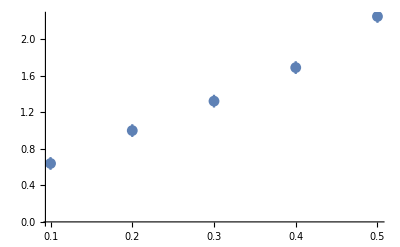

```mathematica
plot3=ErrorListPlot[plotlist]
```

Comparison with the fitted function

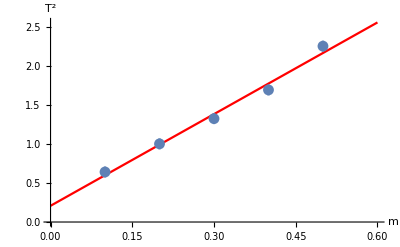

```mathematica
Show[plot2,plot3]
```

shows that we have good agreement.

### Phase 2: SHM and Damped HM

#### Simple Harmonic Motion

Now that you know the values of c and k for your spring, it is time to go back and take some more data as a check. Use a different mass. How does your predicted period compare with your measured period for this mass. What is the amplitude of the motion? What is the phase angle?  When you are satisfied  that your fit makes good predictions, then you may move on.  (Note, though, that I’ll be specifically looking for this kind of check in the Lab Report, so don’t skip it!)

Now put a CD on the weight holder and put some weights on top of the CD. The CD serves to damp the motion due to the air resistance. Repeat the analysis above to find the amplitude, the phase factor and now the damping factor. This is last weeks lab with real data.

As an example consider the data we looked at earlier.

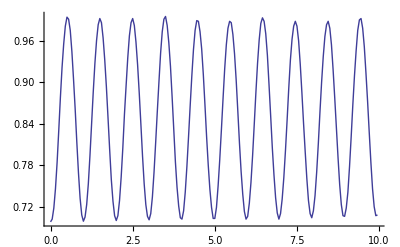

```mathematica
plot4=ListPlot[positionData,Joined->True]
```

Recall that the angular frequency is given by

```mathematica
Clear[c,M,m,k]
ω=√(k/(M+c m))
```

√(k/(c m+M))

We know (from the previous section) that k=10.1 N/m, m=0.173 kg and c=0.31, and the mass of the weight plus the weight holder is M=.2 kg, so we can calculate ω

```mathematica
k=10.1;
m=0.173;
M=0.2;
c=0.31;
ω
```

6.31045

We can now use the function Fit to fit our data to combination of sines and cosines. We have to remember to include a linear term in our fit since this term will fix the initial release point of the oscillator.

```mathematica
f2=Fit[positionData,{1,Sin[ω t],Cos[ω t]},t]
```

0.00652942 sin(6.31045 t)-0.144243 cos(6.31045 t)+0.845979

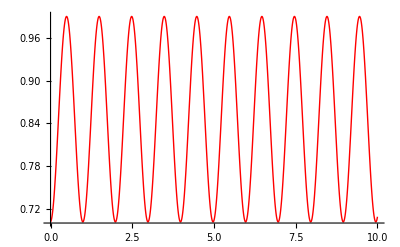

```mathematica
plot5=Plot[f2,{t,0,10},PlotStyle->RGBColor[1,0,0]]
```

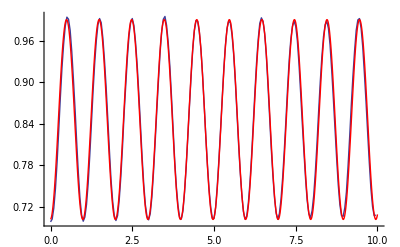

```mathematica
Show[plot4,plot5]
```

#### Damped Harmonics

When analyzing your damped harmonic motion data keep in mind that you can use your mouse to pick of the peaks of your damped data. You can then fit the peaks (using NonlinearFit) to ⅇ^(-γ t/2). This will give you γ. This is illustrated below.

This “Import” statement is not expected to work; it (and the statements below which depend on it) is (are) only included so that you see what the code looks like.  Your statements can be based on these, but will be changed somewhat.

```mathematica
dampedData=Import["/Users/gass/Desktop/damped.csv"];
```

```mathematica
positionData=Table[{dampedData⟦i,1⟧,dampedData⟦i,2⟧},{i,1,Length[dampedData]}];
```

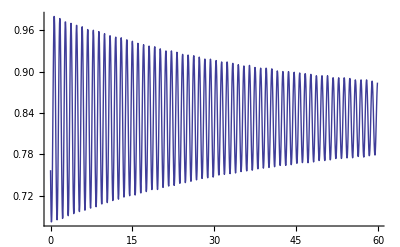

```mathematica
dampedPlot=ListPlot[positionData,Joined->True]
```

Using the ability to track points on the curve, we will extract the position of the peaks. The result is below.

```mathematica
peaks={{0.211464,0.935688},{1.30155,0.935688},{2.11911,0.93221},{3.2092,0.929428},{4.1176,0.925254},{5.11685,0.923168},{6.29777,0.921776},{7.11534,0.920385},{8.29626,0.914821},{9.11383,0.916212},{10.1131,0.910647},{11.2032,0.909952},{12.1116,0.907865},{13.2016,0.907169},{14.2009,0.903691},{15.2001,0.9023},{16.1994,0.899518},{17.1986,0.898127},{18.1979,0.893953},{19.1971,0.891867},{20.2872,0.88978},{21.2864,0.88978},{22.2857,0.886998},{23.2849,0.886302},{24.1933,0.884911},{25.1926,0.88352},{26.1918,0.882128},{27.2819,0.880737},{28.0995,0.878651},{29.3712,0.875868},{30.1888,0.874477},{31.3697,0.873086},{32.2781,0.870304},{33.2774,0.869608},{34.1858,0.868913},{35.2759,0.86613},{36.2751,0.865435},{37.3652,0.865435},{38.2736,0.864739},{39.2729,0.861261},{40.0904,0.860566},{41.2713,0.858479},{42.1797,0.85987},{43.2698,0.857088},{44.1782,0.857088},{45.2683,0.855001},{46.1767,0.854305},{47.176,0.852219},{48.1752,0.850828},{49.3561,0.852219},{50.1737,0.850132},{51.0821,0.848741},{52.0814,0.84735},{53.2623,0.848045},{54.2615,0.845263},{55.2608,0.844567},{56.26,0.842481},{57.2593,0.843176},{58.2585,0.841785},{59.2578,0.841089}};
```

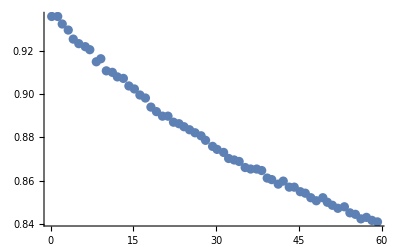

```mathematica
plot6=ListPlot[peaks]
```

To do the Fitting we use FindFit.  The output is different from NonLinearModelFit: FindFit gives a list of replacement rules for the parameters, while NonLinearModelFit returns the full function with the best-fit parameters inserted.

Our model will be:

a ⅇ^(-(γ t)/2)+d

where a is the initial amplitude and d is the displacement.  Because the origin is not necessarily at x=0, we need the d term so

```mathematica
result=FindFit[peaks,a ⅇ^(-(γ t)/2)+d,{{a,1},{γ,0.05}, {d, .91}},t]
```

{a→0.139844,γ→0.0394882,d→0.797732}

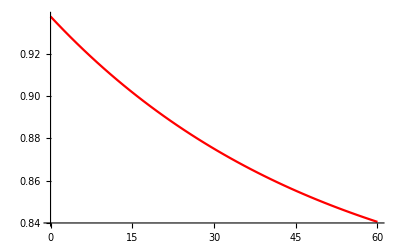

```mathematica
plot7=Plot[(a ⅇ^(-1/2 (γ t))+d)/.result,{t,0,60},PlotStyle->RGBColor[1,0,0]]
```

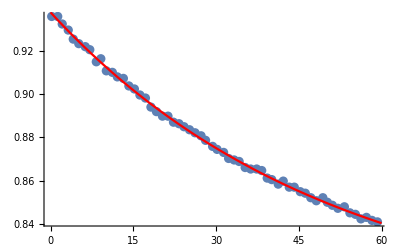

```mathematica
Show[plot6,plot7]
```

As you can see it is a good fit.
So we have that
d≈.80
a≈.14
γ≈.038

Now we will use FindFit to finish the job.  First let's remember our model:

A ⅇ^(-γ/2t)Cos[√(w^2-γ^2/4)t+ϕ]+d

Now we will again use FindFit.

```mathematica
k=10.1;
m=0.173;
M=0.2;
c=0.31;
ω=√(k/(M+c m));
```

We are using w, so that we don't have to clear ω but we do have to clear A and ϕ.

```mathematica
Clear[ϕ,A]
values=FindFit[positionData,A ⅇ^(-γ/2 t)Cos[√(w^2-γ^2/4)t+ϕ]+d,{{A,.13},{γ,0.05}, {d, .85}, {w,ω}, {ϕ, -π/2}},t]
```

{A→-0.147662,γ→0.0358853,d→0.832094,w→6.14925,ϕ→-1.10132}

```mathematica
result2=(A ⅇ^(-γ/2 t)Cos[√(w^2-γ^2/4)t+ϕ]+d)/.values
```

0.832094-0.147662 ⅇ^(-0.0179427 t) cos(1.10132-6.14922 t)

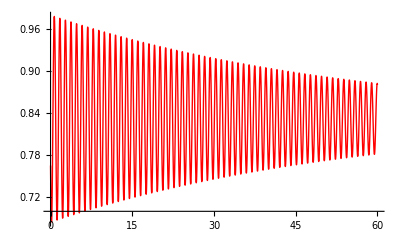

```mathematica
plot10=Plot[result2,{t,0,60},PlotPoints->200,PlotStyle->RGBColor[1,0,0]]
```

If the results don't match up, the first thing one should try is changing the values of the guesses.  However, in our example the fit is quite good.

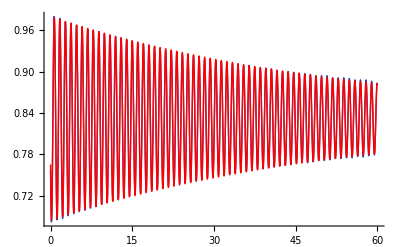

```mathematica
Show[dampedPlot,plot10,PlotRange->All]
```

### One last Experiment

Pick one of the masses that you used in part one (the measurement of c and k). Now turn the spring upside down. That is hang it large end up. Measure the period. Can you explain what happens?

## Upshot

This is a rough outline of the experiment.  This is not necessarily a complete list of what needs to be done.

1) Take four datasets (using four different masses), find the period squared for each.

2) Take a fifth dataset that has a different mass from the previous four.  This will allow us to check our results.

3) Use a CD to make a damped harmonic oscillator and calculate the damping coefficient (γ), as well as the angular frequency (ω), the phase angle (ϕ), and the amplitude (A).

4) Take a final data set with the spring the other way round, and comment on the results.

## Assignment

The assignment for Week 15 is a full Lab Report which addresses all relevant questions and results from this writeup, and reflects on each.  This report should be written in accordance with the general rules and guidelines of the Syllabus for this course; please ask if there are any questions about what specifically is required.